#### Very simple neural network: Classify points in x,y plane with x and y as inputs - SR 22Jun18

```mathematica
neurons=4;
```

Each of the neurons has two input weights, a bias an an output weight

```mathematica
variables=Table[{w1[j],w2[j],wo[j],b[j]},{j,neurons}]//Flatten
```

{w1[1],w2[1],wo[1],b[1],w1[2],w2[2],wo[2],b[2],w1[3],w2[3],wo[3],b[3],w1[4],w2[4],wo[4],b[4]}

```mathematica
ini:=state=#->RandomReal[{-1,1}]&/@variables
```

```mathematica
ini;state
```

{w1[1]→0.516038,w2[1]→0.504167,wo[1]→-0.724541,b[1]→0.682087,w1[2]→-0.776543,w2[2]→-0.672453,wo[2]→0.563755,b[2]→-0.369543,w1[3]→0.0503961,w2[3]→-0.800604,wo[3]→0.377181,b[3]→0.771926,w1[4]→0.579021,w2[4]→0.528575,wo[4]→0.0851971,b[4]→-0.15293}

The output of a single neuron is the activation function of the sum of the weighted inputs minus the bias:

```mathematica
z[i_]:=w1[i]*x+w2[i]*y-b[i]
```

```mathematica
output:=Sum[wo[j]/(1+Exp[-z[j]]),{j,neurons}]
```

The output of the network depends on the coordinates x,y and the weights and biases:

```mathematica
output
```

wo[1]/(1+ⅇ^(b[1]-x w1[1]-y w2[1]))+wo[2]/(1+ⅇ^(b[2]-x w1[2]-y w2[2]))+wo[3]/(1+ⅇ^(b[3]-x w1[3]-y w2[3]))+wo[4]/(1+ⅇ^(b[4]-x w1[4]-y w2[4]))

```mathematica
Block[{x=-4,y=4},output/.state]
```

0.198852

```mathematica
plot:=ContourPlot[output/.state,{x,-5,5},{y,-5,5}]
```

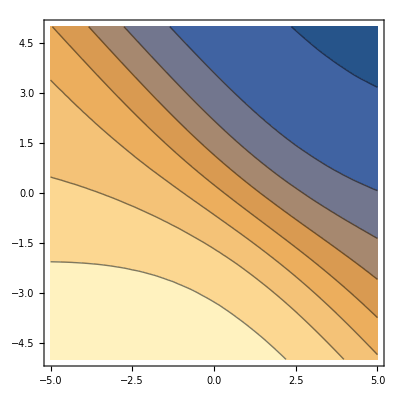

```mathematica
plot
```

Training data: We will take 100 random points and ±1 depending on their quadrant:

```mathematica
training=Table[{xtemp=RandomReal[{-5,5}],ytemp=RandomReal[{-5,5}],Sign[xtemp*ytemp]},{i,100}];
```

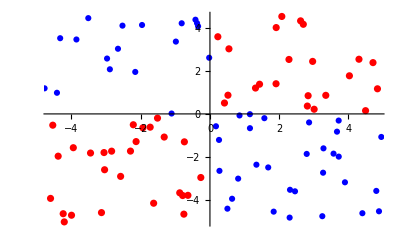

```mathematica
trainplot=Show[ListPlot[If[#[[3]]>0,{#[[1]],#[[2]]}]&/@training,PlotStyle->Red],ListPlot[If[#[[3]]<0,{#[[1]],#[[2]]}]&/@training,PlotStyle->Blue]]
```

The loss (or cost) function is almost like χ^2: Sum the deviation over the (training) data:

```mathematica
loss=Total[(#[[3]]-(output/.{x->#[[1]],y->#[[2]]}))^2&/@training];
```

```mathematica
loss
```

(-1-wo[1]/(1+ⅇ^(b[1]+3.2312 w1[1]-4.87438 w2[1]))-wo[2]/(1+ⅇ^(b[2]+3.2312 w1[2]-4.87438 w2[2]))-wo[3]/(1+ⅇ^(b[3]+3.2312 w1[3]-4.87438 w2[3]))-wo[4]/(1+ⅇ^(b[4]+3.2312 w1[4]-4.87438 w2[4])))^2+(1-wo[1]/(1+ⅇ^(b[1]-2.07553 w1[1]-4.51179 w2[1]))-wo[2]/(1+ⅇ^(b[2]-2.07553 w1[2]-4.51179 w2[2]))-wo[3]/(1+ⅇ^(b[3]-2.07553 w1[3]-4.51179 w2[3]))-wo[4]/(1+ⅇ^(b[4]-2.07553 w1[4]-4.51179 w2[4])))^2+97+(1-wo[1]/(1+ⅇ^(b[1]+4.20611 w1[1]+4.99934 w2[1]))-wo[2]/(1+ⅇ^(b[2]+4.20611 w1[2]+4.99934 w2[2]))-wo[3]/(1+ⅇ^(b[3]+4.20611 w1[3]+4.99934 w2[3]))-wo[4]/(1+ⅇ^(b[4]+4.20611 w1[4]+4.99934 w2[4])))^2
 |  |  |  |

```mathematica
loss/.state
```

128.691

To train the network, we need to do a gradient descent, i.e. replace w1[1] by

```mathematica
(w1[1]/.state)-η D[loss,w1[1]]/.state
```

0.516038-0.704594 η

Do this for 20% of all the variables:

```mathematica
update:=#->(#/.state)-If[RandomReal[]<.2,η (D[loss,#]/.state),0]&/@variables
```

```mathematica
update
```

{w1[1]→0.516038,w2[1]→0.504167,wo[1]→-0.724541,b[1]→0.682087-9.94223 η,w1[2]→-0.776543,w2[2]→-0.672453,wo[2]→0.563755,b[2]→-0.369543,w1[3]→0.0503961,w2[3]→-0.800604,wo[3]→0.377181,b[3]→0.771926,w1[4]→0.579021,w2[4]→0.528575,wo[4]→0.0851971,b[4]→-0.15293+1.60509 η}

Run this for a while:

```mathematica
Manipulate[Block[{η=.01,dummy=i},state=update;Show[plot,trainplot,PlotLabel->loss/.state]],{i,100,1}]
```

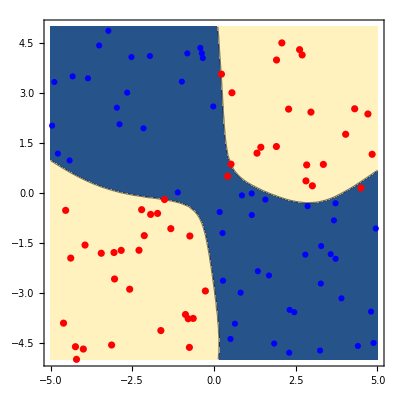

```mathematica
Show[ContourPlot[output/.state,{x,-5,5},{y,-5,5},Contours->{0}],trainplot]
```